## Ringdown parametrizations

The general ringdown model native to BH perturbation theory is written in terms of a SWSH decomposition. Assuming PT symmetry, the most general form of a given (ℓ,|m|,n) mode is
	h_n=C_(ℓ m n)e^(-i (ω̃)_(ℓ m n)t)+C_(ℓ -m n)e^(-i ((ω̃)_(ℓ m n))^*t)≡ C_(R,n)e^(-i ((ω̃)_n t-ϕ_(R,n)))+C_(L, n)e^(i (((ω̃)_n)^*t+ϕ_(L,n))) ,
where the C_(ℓ ±m n)≡C_(R/L,n) e^(iϕ_(R/L,n)) are complex valued, but C_(R/L,n) are real. This is clearly written in terms of circular, R/L modes. We can rewrite this in terms of an ellipticity and related angles as follows:
	h_n=1/2 A_n e^(-t/τ_n)[(1+ϵ_n) e^(-i (ω_n t-ϕ_(R,n)))+(1-ϵ_n) e^(i (ω_n t+ϕ_(L,n)))] ,
or, equivalently,
	h_n=A_n[cosθ_n cos(ω_n t-ϕ_n) - ϵ_n sinθ_n sin(ω_n t-ϕ_n)]e^(-t/τ_n) - i A_n[sinθ_n cos(ω_n t-ϕ_n) + ϵ_n cosθ_n sin(ω_n t-ϕ_n)] e^(-t/τ_n) .

With some algebra, we can show this to be equivalent to a template based on linear modes,
	h_n= ((A^+)_(n,x)cos ω_n t + (A^+)_(n,y)sin ω_n t)e^(-t/τ_n)-i ((A^×)_(n,x)cos ω_n t + (A^×)_(n,y)sin ω_n t)e^(-t/τ_n),
which is the same as
	h_n= (A^+)_n cos (ω_n t -(φ^+)_n) e^(-t/τ_n) - i (A^×)_n cos (ω_n t -(φ^×)_n)e^(-t/τ_n).

### Coordinate transformations

The relevant coordinate transformations are as follows, suppressing the n index.

```mathematica
AepToCphi={
A-> CR+CL,
ϵ-> (CR -CL)/(CR+CL),
ϕ->(ϕR-ϕL)/2,
θ->-(ϕR+ϕL)/2
};
CphiToAep={
CR->1/2 A (1+ϵ),
CL->1/2 (A-A ϵ),
ϕR->ϕ-θ,
ϕL->-(θ+ϕ)
};
```

```mathematica
AphiToAxAy={
Ap->√(Apx^2+Apy^2),
Ac->√(Acx^2+Acy^2),
φp->ArcTan[Apx,Apy],
φc->ArcTan[Acx,Acy]
};
AxAyToAphi={
Apx->Ap Cos[φp],
Apy->Ap Sin[φp],
Acx->Ac Cos[φc],
Acy->Ac Sin[φc]
};

AxAyToCphi={
Apx->CR Cos[ϕR]+CL Cos[ϕL],
Apy->CR Sin[ϕR]-CL Sin[ϕL],
Acx->-CR Sin[ϕR]-CL Sin[ϕL],
Acy->CR Cos[ϕR]-CL Cos[ϕL]
};
```

Let’s find the inverse transformation for the last set:

```mathematica
Assuming[{Element[{Apx,Apy,Acx,Acy},Reals],CR>0,CL>0,0≤ϕR≤2π,0≤ϕL≤2π},
FullSimplify[Solve[Equal@@@Flatten[AxAyToCphi],{CR,CL,ϕR,ϕL}]]]
```

{{CR→-1/2 √((Acy+Apx)^2+(Acx-Apy)^2),CL→-1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϕR→ConditionalExpression[ArcTan[-Acy-Apx,Acx-Apy]+2 π C[2], C[2]∈ℤ],ϕL→ConditionalExpression[ArcTan[Acy-Apx,Acx+Apy]+2 π C[1], C[1]∈ℤ]},{CR→-1/2 √((Acy+Apx)^2+(Acx-Apy)^2),CL→1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϕR→ConditionalExpression[ArcTan[-Acy-Apx,Acx-Apy]+2 π C[2], C[2]∈ℤ],ϕL→ConditionalExpression[ArcTan[-Acy+Apx,-Acx-Apy]+2 π C[1], C[1]∈ℤ]},{CR→1/2 √((Acy+Apx)^2+(Acx-Apy)^2),CL→-1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϕR→ConditionalExpression[ArcTan[Acy+Apx,-Acx+Apy]+2 π C[2], C[2]∈ℤ],ϕL→ConditionalExpression[ArcTan[Acy-Apx,Acx+Apy]+2 π C[1], C[1]∈ℤ]},{CR→1/2 √((Acy+Apx)^2+(Acx-Apy)^2),CL→1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϕR→ConditionalExpression[ArcTan[Acy+Apx,-Acx+Apy]+2 π C[2], C[2]∈ℤ],ϕL→ConditionalExpression[ArcTan[-Acy+Apx,-Acx-Apy]+2 π C[1], C[1]∈ℤ]}}

Unsurprisingly, there are multiple solutions. This shouldn’t matter for the Jacobian, so let’s take the one in the positive (x, y) quadrant for now

```mathematica
CphiToAxAy={
CR->1/2 √((Acy+Apx)^2+(Acx-Apy)^2),
CL->1/2 √((Acy-Apx)^2+(Acx+Apy)^2),
ϕR->ArcTan[Acy+Apx,-Acx+Apy],
ϕL->ArcTan[-Acy+Apx,-Acx-Apy]
};
```

The corresponding transformation to (A, φ) is:

```mathematica
CphiToAphi=Assuming[{Ac>0,Ap>0,Element[{ϕp,ϕc},Reals]},FullSimplify[CphiToAxAy//.AxAyToAphi]]
```

{CR→1/2 √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]),CL→1/2 √(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]),ϕR→ArcTan[Ap Cos[φp]+Ac Sin[φc],-Ac Cos[φc]+Ap Sin[φp]],ϕL→ArcTan[Ap Cos[φp]-Ac Sin[φc],-Ac Cos[φc]-Ap Sin[φp]]}

We will also want to be able to go directly from linear quadratures to the elliptic parameterization (or vice-versa):

```mathematica
AepToAxAy =AepToCphi//.CphiToAxAy
```

{A→1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2),ϵ→(1/2 √((Acy+Apx)^2+(Acx-Apy)^2)-1/2 √((Acy-Apx)^2+(Acx+Apy)^2))/(1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2)),ϕ→1/2 (-ArcTan[-Acy+Apx,-Acx-Apy]+ArcTan[Acy+Apx,-Acx+Apy]),θ→1/2 (-ArcTan[-Acy+Apx,-Acx-Apy]-ArcTan[Acy+Apx,-Acx+Apy])}

#### Transformation checks

Let’s check that the above transformations return the expected expressions for h, ignoring exponential damping term.

```mathematica
hRL=CR Exp[I ϕR] Exp[-I ωt]+CL Exp[I ϕL] Exp[I ωt];
```

In terms of an ellipticity, the complex-valued strain should look like h=1/2 A [(1+ϵ) e^(-i (ωt-ϕ_R))+(1-ϵ) e^(i (ω_n t+ϕ_L))] , with ϕ_R=ϕ-θ and  ϕ_L=-ϕ-θ

```mathematica
hAep = hRL//.CphiToAep
```

1/2 A ⅇ^(ⅈ (-θ+ϕ)-ⅈ ωt) (1+ϵ)+1/2 ⅇ^(ⅈ (-θ-ϕ)+ⅈ ωt) (A-A ϵ)

Look at the corresponding plus and cross polarizations, which should take the form
	h_+=A [cosθ cos(ωt-ϕ) - ϵ sinθ  sin(ωt-ϕ)] 
	h_×=A [sinθ cos(ωt-ϕ) + ϵ cosθ  sin(ωt-ϕ)]

```mathematica
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[Re[hAep]]]]
Assuming[{Element[{A,θ,ϕ,ϵ,ωt},Reals]},FullSimplify[ComplexExpand[-Im[hAep]]]]
```

A (Cos[θ] Cos[ϕ-ωt]+ϵ Sin[θ] Sin[ϕ-ωt])

A (Cos[ϕ-ωt] Sin[θ]-ϵ Cos[θ] Sin[ϕ-ωt])

Now, focus on the cos and sin quadratures of the linear polarizations. First, check that we get the right expressions starting from h= A^+cos (ωt -φ^+) - i A^×cos (ωt -φ^×)

```mathematica
hAphi = Ap Cos[ωt -φp]-I Ac Cos[ωt -φc];
hAphi//.AphiToAxAy
```

-ⅈ √(Acx^2+Acy^2) Cos[ωt-ArcTan[Acx,Acy]]+√(Apx^2+Apy^2) Cos[ωt-ArcTan[Apx,Apy]]

Simplifying, we should get  h=((A^+)_x cos ωt+(A^+)_y sin ωt)-i((A^×)_x cos ωt+(A^×)_y sin ωt)

```mathematica
hAxAy=ComplexExpand[FullSimplify[hAphi//.AphiToAxAy]]
```

Apx Cos[ωt]+Apy Sin[ωt]+ⅈ (-Acx Cos[ωt]-Acy Sin[ωt])

We should be able to re-express this in terms of the original R/L modes, i.e. h=C_R e^(-i (ωt-ϕ_R))+C_L e^(i (ωt+ϕ_L))

```mathematica
TrigToExp[hAxAy//.AxAyToCphi]
TrigToExp[hAxAy//.AxAyToCphi] - hRL
```

CR ⅇ^(ⅈ ϕR-ⅈ ωt)+CL ⅇ^(ⅈ ϕL+ⅈ ωt)

0

The inverse transformation is

```mathematica
ComplexExpand[FullSimplify[hRL//.CphiToAxAy]]
ComplexExpand[FullSimplify[hRL//.CphiToAxAy]] - hAxAy
```

Apx Cos[ωt]+Apy Sin[ωt]+ⅈ (-Acx Cos[ωt]-Acy Sin[ωt])

0

Or, straight to (A,φ),

```mathematica
ComplexExpand[FullSimplify[hRL//.CphiToAphi]]
ComplexExpand[FullSimplify[hRL//.CphiToAphi]]-hAphi
```

-ⅈ Ac Cos[φc-ωt]+Ap Cos[φp-ωt]

0

Just to be extra sure, double check the intermediate expression for R/L modes in terms of linear polarizations and cos/sin quadratures:

```mathematica
ComplexExpand[TrigExpand[ExpToTrig[hRL]]]
```

CL Cos[ϕL] Cos[ωt]+CR Cos[ϕR] Cos[ωt]-CL Sin[ϕL] Sin[ωt]+CR Sin[ϕR] Sin[ωt]+ⅈ (CL Cos[ωt] Sin[ϕL]+CR Cos[ωt] Sin[ϕR]+CL Cos[ϕL] Sin[ωt]-CR Cos[ϕR] Sin[ωt])

### Jacobians

Now that we’ve nailed down the transformations between all possible parametrizations, let’s compute some Jacobians.

First, since we will be sampling in ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y), we want to know what a uniform prior on those quantities implies for (A,ϵ), without really caring about the (θ,ϕ) angles. We want to compute the following Jacobian:
	J = |(∂(A, ϵ, θ, ϕ))/(∂((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y))|

```mathematica
Aeps = {A,ϵ,θ,ϕ};
Axys = {Apx,Apy,Acx,Acy};
```

```mathematica
d=Assuming[Element[Aeps,Reals],FullSimplify[Det[D[Aeps//.AepToAxAy,{Axys}]]]]
```

-(2/(√((Acy+Apx)^2+(Acx-Apy)^2) √((Acy-Apx)^2+(Acx+Apy)^2) (√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))))

```mathematica
J=Assuming[{CL>0,CR>0,A>0,-1<=ϵ<=1},FullSimplify[Abs[d]//.AxAyToCphi//.CphiToAep]]
```

1/(A^3-A^3 ϵ^2)

```mathematica
PowerExpand@Log[J]
```

-Log[A^3-A^3 ϵ^2]

```mathematica
FullSimplify[PowerExpand@Log[-d],Element[Aeps,Reals]]
```

Log[2]-1/2 Log[(Acy+Apx)^2+(Acx-Apy)^2]-1/2 Log[(Acy-Apx)^2+(Acx+Apy)^2]-Log[√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2)]

As a sanity check, let’s make sure that we get the right Jacobian in going from ((A^+)_x,(A^+)_y,(A^×)_x,(A^×)_y) to (A^+,A^×,φ^+,φ^×), i.e. J=1/(A^+A^×)

```mathematica
Aphi={Ap,Ac,φp,φc};
```

```mathematica
Assuming[{Ap>0,Ac>0,Element[Aphi,Reals]},FullSimplify[
Abs[Det[D[Aphi//.AphiToAxAy,{Axys}]]]//.AxAyToAphi]]
```

1/(Ac Ap)

Also compute the Jacobian between plus and cross and A ellip

```mathematica
AphiToAep = AphiToAxAy//.AxAyToCphi//.CphiToAep;
AepToAphi = Simplify[AepToCphi//.CphiToAphi];
```

```mathematica
J2=Assuming[{Ap>0,Ac>0, Element[Aphi,Reals]},FullSimplify[
Abs[Det[D[Aeps//.AepToAphi,{Aphi}]]]]]
```

(2 Ac Ap)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]) (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])))

```mathematica
PowerExpand@Log[J2]
```

Log[2]+Log[Ac]+Log[Ap]-1/2 Log[Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]]-Log[√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])]

```mathematica
J2b = FullSimplify[J2//.AphiToAep, Element[Aeps,Reals]&&A>0&&-1<ϵ<1]
```

(√(((1+ϵ^2)^2)/((-1+ϵ^2)^2)-Cos[2 θ]^2))/(2 A)

```mathematica
FortranForm[J2b]
```

Sqrt((1 + ϵ**2)**2/(-1 + ϵ**2)**2 - Cos(2*θ)**2)/(2.*A)

```mathematica
PowerExpand@Log[J2b]
```

-Log[2]-Log[A]+1/2 Log[((1+ϵ^2)^2)/((-1+ϵ^2)^2)-Cos[2 θ]^2]

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0,FullSimplify[TrigToExp[Cos[2θ]//.AepToAphi]]]
```

(-Ac^2+Ap^2)/(√(Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]))

```mathematica
Assuming[Element[Aphi,Reals]&&Ap>0&&Ac>0,FullSimplify[TrigToExp[Cos[ϕ]//.AepToAphi]]]
```

(Ap ⅇ^(ⅈ φp) √(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+Ac (-ⅈ Cos[φc]+Sin[φc]) √(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])-ⅈ Ac ⅇ^(-ⅈ φc) √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp])+Ap ⅇ^(-ⅈ φp) √(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))/(2 √(-(ⅈ (Ac^4+Ap^4+2 Ac^2 Ap^2 Cos[2 φc-2 φp]) √(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp]))/(Ac ⅇ^(ⅈ φc)-ⅈ Ap Cos[φp]+Ap Sin[φp])) √((√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]) (-ⅈ Cos[φc+φp]+Sin[φc+φp]))/(Ac ⅇ^(ⅈ φp)-ⅈ Ap Cos[φc]+Ap Sin[φc])))

### Plots

#### Jacobians

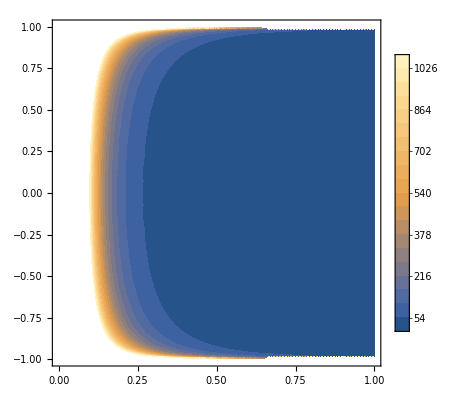

```mathematica
ContourPlot[1/(A^3-A^3 ϵ^2),{A,0,1},{ϵ,-1,1},Contours->20,ContourStyle->None, PlotLegends->Automatic]
```

```mathematica
Plot3D[1/(A^3-A^3 ϵ^2),{A,0,1},{ϵ,-1,1},AxesLabel->{"A","ϵ","J"}]
```

-Graphics3D-

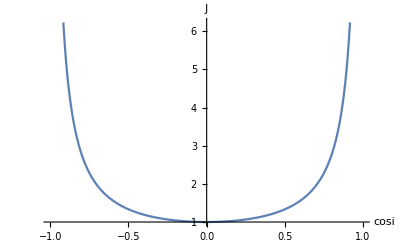

```mathematica
Plot[1/(A^3-A^3 ϵ^2)/.{A->1},{ϵ,-1,1},AxesLabel->{"cosi","J"}]
```

#### Coordinate transformations

```mathematica
Simplify[ϵ//.AepToAxAy]
```

(√((Acy+Apx)^2+(Acx-Apy)^2)-√((Acy-Apx)^2+(Acx+Apy)^2))/(√((Acy+Apx)^2+(Acx-Apy)^2)+√((Acy-Apx)^2+(Acx+Apy)^2))

```mathematica
Simplify[ϵ//.AepToCphi//.CphiToAphi//.{Ap->1,Ac->1}]
```

(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))

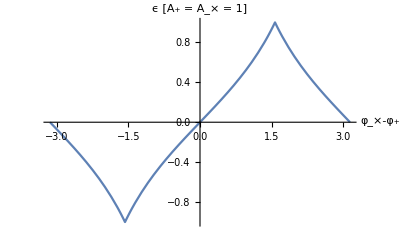

```mathematica
Plot[(-√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/(√(1-Sin[φc-φp])+√(1+Sin[φc-φp]))/.(φc-φp)->Δφ,{Δφ,-Pi,Pi},AxesLabel->{"φ_×-φ_+","ϵ [A_+ = A_× = 1]"}]
```

```mathematica
FullSimplify[A//.AepToAxAy//.AxAyToAphi,Element[Axys,Reals]]
```

1/2 (√(Ac^2+Ap^2-2 Ac Ap Sin[φc-φp])+√(Ac^2+Ap^2+2 Ac Ap Sin[φc-φp]))

```mathematica
FullSimplify[J-(-3*Log[A]-Log[1-ϵ^2]),A>0&&-1≤ϵ<1]
```

1/(A^3-A^3 ϵ^2)+3 Log[A]+Log[1-ϵ^2]

```mathematica
FullSimplify[{ϕ,θ}//.AepToCphi]
```

{1/2 (-ϕL+ϕR),1/2 (-ϕL-ϕR)}

```mathematica
FullSimplify[{ϕR,ϕL}//.CphiToAxAy]
```

{ArcTan[Acy+Apx,-Acx+Apy],ArcTan[-Acy+Apx,-Acx-Apy]}

```mathematica
FullSimplify[FullSimplify[A//.AepToCphi//.CphiToAphi//.{φp->ϕ,φc->ϕ-Pi/2}]//.{Ap->(1+cosi^2)A,Ac->2 cosi A},A>0&&-1<cosi<1]
```

A (1+cosi^2)

```mathematica
FullSimplify[FullSimplify[ϵ//.AepToCphi//.CphiToAphi//.{φp->ϕ,φc->ϕ-Pi/2}]//.{Ap->(1+cosi^2)A,Ac->2 cosi A},A>0&&-1<cosi<1]
```

-(2 cosi)/(1+cosi^2)

```mathematica
Solve[ϵ==-(2 cosi)/(1+cosi^2), cosi]
```

{{cosi→(-1-√(1-ϵ^2))/ϵ},{cosi→(-1+√(1-ϵ^2))/ϵ}}

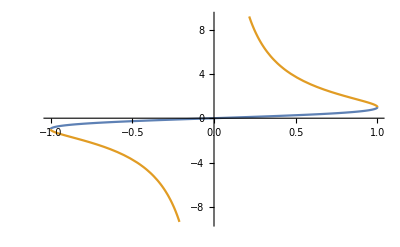

```mathematica
Plot[{(1-√(1-ϵ^2))/ϵ,(1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

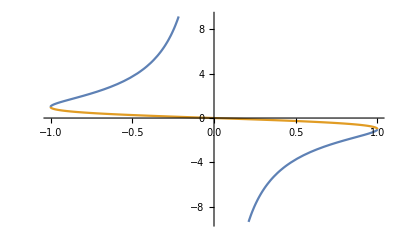

```mathematica
Plot[{(-1-√(1-ϵ^2))/ϵ,(-1+√(1-ϵ^2))/ϵ},{ϵ,-1,1}]
```

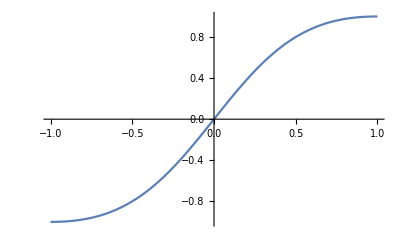

```mathematica
Plot[(2 cosi)/(1+cosi^2),{cosi,-1,1}]
```

```mathematica
Jcosi = FullSimplify[Abs[D[(-1+√(1-ϵ^2))/ϵ,ϵ]],-1<ϵ<1]
```

(-1+1/(√(1-ϵ^2)))/ϵ^2

```mathematica
ϵ^2//.AepToAxAy
```

((1/2 √((Acy+Apx)^2+(Acx-Apy)^2)-1/2 √((Acy-Apx)^2+(Acx+Apy)^2))^2)/((1/2 √((Acy+Apx)^2+(Acx-Apy)^2)+1/2 √((Acy-Apx)^2+(Acx+Apy)^2))^2)

```mathematica
FullSimplify[Jcosi //. ϵ->(2 cosi)/(1+cosi^2),-1<cosi<1]
```

-((1+cosi^2)^2)/(2 (-1+cosi^2))

```mathematica
PowerExpand@Log[Jcosi]
```

-2 Log[ϵ]+Log[-1+1/(√(1-ϵ^2))]

```mathematica
FullSimplify[Abs[D[(1-√(1-ϵ^2))/ϵ,ϵ]],-1<ϵ<1]
```

(-1+1/(√(1-ϵ^2)))/ϵ^2

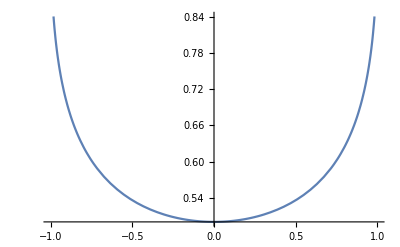

```mathematica
Plot[Abs[(-1+√(1-ϵ^2))/ϵ^2],{ϵ,-1,1}]
```

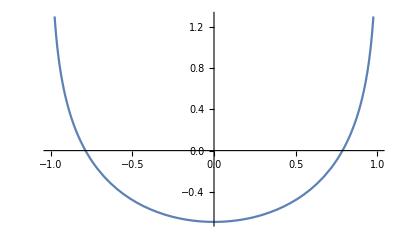

```mathematica
Plot[-2 Log[Abs[ϵ]]+Log[Abs[-1+1/(√(1-ϵ^2))]],{ϵ,-1,1}]
```

```mathematica
FullSimplify[Abs[(-1+√(1-ϵ^2))/ϵ^2], -1<ϵ<1]
```

Abs[(-1+√(1-ϵ^2))/ϵ^2]

```mathematica
Log[-1/ϵ^2]
```

Log[-1/ϵ^2]

```mathematica
FortranForm[FullSimplify[ϕ//.AepToAxAy]]
```

(-ArcTan(-Acy + Apx,-Acx - Apy) + 
     -    ArcTan(Acy + Apx,-Acx + Apy))/2.